Start with the data from Kissel, Quarles &  Pratt.

```mathematica
Clear[raw,kissel,S,γ,β,Acosta, bestAB]
```

```mathematica
kissel={{1,2,0.00,1.00283,-0.21151,0.17523,-0.01017,0.00003,0.00000},{1,2,0.60,0.99589,-0.08591,-0.59025,0.01747,0.00062,0.00017},{1,2,0.80,0.99419,-0.05333,-0.80182,0.02101,0.00069,0.00024},{1,2,0.95,0.99308,-0.03139,-0.95045,0.02314,0.00041,0.00031},{1,8,0.00,1.00327,-0.20609,0.02951,-0.00243,0.00001,0.00000},{1,8,0.60,0.99785,-0.10855,-0.56474,0.02936,0.00252,-0.00014},{1,8,0.80,0.99681,-0.08863,-0.69444,0.03411,0.00325,-0.00017},{1,8,0.95,0.99619,-0.07663,-0.77359,0.03705,0.00253,-0.00010},{1,13,0.00,1.00365,-0.20121,-0.10160,0.00943,-0.00025,0.00000},{1,13,0.60,0.99920,-0.12071,-0.59570,0.04347,0.00141,-0.00014},{1,13,0.80,0.99833,-0.10563,-0.68214,0.04725,-0.00020,0.00005},{1,13,0.95,0.99779,-0.09638,-0.73304,0.04887,0.00008,0.00047},{1,47,0.00,1.00480,-0.18676,-0.49059,0.07122,-0.00460,0.00020},{1,47,0.60,1.00188,-0.14121,-0.71105,0.09273,-0.00664,-0.00058},{1,47,0.80,1.00202,-0.14223,-0.71696,0.09391,-0.00475,-0.00025},{1,47,0.95,1.00259,-0.14796,-0.72188,0.09995,-0.00618,0.00028},{1,79,0.00,1.00488,-0.18581,-0.51588,0.06850,-0.00373,0.00013},{1,79,0.60,1.00320,-0.16373,-0.58320,0.07512,-0.00358,-0.00215},{1,79,0.80,1.00360,-0.16957,-0.55865,0.07451,-0.00534,0.00065},{1,79,0.95,1.00348,-0.16884,-0.55066,0.07219,-0.00379,0.00025},{1,92,0.00,1.00466,-0.18850,-0.44352,0.05487,-0.00263,0.00008},{1,92,0.60,1.00285,-0.16409,-0.52443,0.06063,-0.00345,-0.00254},{1,92,0.80,1.00363,-0.17369,-0.50279,0.06351,-0.00329,-0.00128},{1,92,0.95,1.00506,-0.18934,-0.49102,0.06918,-0.00553,0.00288},{5,2,0.00,1.01192,-0.46909,0.28693,-0.02403,-0.00016,0.00000},{5,2,0.60,0.97473,-0.17091,-0.56724,0.02152,0.00117,0.00198},{5,2,0.80,0.96784,-0.10490,-0.78669,0.02935,0.00171,0.00281},{5,2,0.95,0.96307,-0.05779,-0.94635,0.03549,0.00082,0.00374},{5,8,0.00,1.01292,-0.46403,0.22465,-0.02137,0.00006,0.00001},{5,8,0.60,0.97955,-0.19769,-0.54140,0.03240,0.00123,0.00151},{5,8,0.80,0.97338,-0.14082,-0.72552,0.04108,0.00142,0.00211},{5,8,0.95,0.96922,-0.10116,-0.85693,0.04673,0.00064,0.00257},{5,13,0.00,1.01373,-0.45993,0.17414,-0.01814,0.00016,0.00001},{5,13,0.60,0.98324,-0.21740,-0.52585,0.04164,0.00112,0.00118},{5,13,0.80,0.97767,-0.16772,-0.68286,0.05087,0.00106,0.00162},{5,13,0.95,0.97393,-0.13338,-0.79346,0.05679,0.00048,0.00195},{5,47,0.00,1.01827,-0.43671,-0.11460,0.03807,-0.00357,0.00014},{5,47,0.60,0.99670,-0.26991,-0.59377,0.11035,-0.00634,0.00093},{5,47,0.80,0.99456,-0.25158,-0.65149,0.11837,-0.00694,0.00109},{5,47,0.95,0.99354,-0.24229,-0.68255,0.12294,-0.00740,0.00090},{5,79,0.00,1.02099,-0.42259,-0.29149,0.09680,-0.01278,0.00103},{5,79,0.60,1.00335,-0.29272,-0.64623,0.16387,-0.01775,0.00130},{5,79,0.80,1.00268,-0.28554,-0.67436,0.17043,-0.01879,0.00143},{5,79,0.95,1.00264,-0.28354,-0.68701,0.17387,-0.01951,0.00153},{5,92,0.00,1.02130,-0.42096,-0.31221,0.10657,-0.01485,0.00134},{5,92,0.60,1.00497,-0.30060,-0.64235,0.16990,-0.01979,0.00203},{5,92,0.80,1.00464,-0.29657,-0.65999,0.17602,-0.02126,0.00218},{5,92,0.95,1.00483,-0.29615,-0.66850,0.17964,-0.02207,0.00230},{10,2,0.00,1.02179,-0.64745,0.33754,-0.03338,-0.00039,-0.00001},{10,2,0.60,0.94942,-0.23918,-0.54496,0.02827,0.00177,0.00082},{10,2,0.80,0.93662,-0.14794,-0.77383,0.04150,0.00243,0.00076},{10,2,0.95,0.92745,-0.08019,-0.94598,0.05382,0.00254,0.00025},{10,8,0.00,1.02330,-0.64274,0.29526,-0.03257,-0.00011,0.00001},{10,8,0.60,0.95416,-0.25757,-0.53299,0.03462,0.00283,0.00108},{10,8,0.80,0.94122,-0.16976,-0.74547,0.04741,0.00312,0.00114},{10,8,0.95,0.93296,-0.10898,-0.90126,0.06083,0.00291,0.00059},{10,13,0.00,1.02446,-0.63911,0.26258,-0.03085,0.00007,0.00001},{10,13,0.60,0.95815,-0.27257,-0.52485,0.04107,0.00319,0.00124},{10,13,0.80,0.94868,-0.20420,-0.70347,0.06209,0.00180,0.00018},{10,13,0.95,0.93798,-0.13446,-0.86309,0.06727,0.00288,0.00079},{10,47,0.00,1.03139,-0.61683,0.05977,0.00831,-0.00169,0.00006},{10,47,0.60,0.98276,-0.35398,-0.51928,0.10586,-0.00542,0.00167},{10,47,0.80,0.97725,-0.31981,-0.60136,0.11696,-0.00581,0.00198},{10,47,0.95,0.97457,-0.30162,-0.64874,0.12461,-0.00584,0.00117},{10,79,0.00,1.03676,-0.59910,-0.10419,0.07132,-0.01219,0.00099},{10,79,0.60,0.99501,-0.37796,-0.59419,0.17769,-0.02076,0.00271},{10,79,0.80,0.99252,-0.36008,-0.64482,0.18972,-0.02218,0.00259},{10,79,0.95,0.99216,-0.35977,-0.64143,0.19061,-0.02317,0.00249},{10,92,0.00,1.03788,-0.59531,-0.13971,0.09036,-0.01712,0.00174},{10,92,0.60,0.99820,-0.38559,-0.60691,0.19926,-0.02760,0.00313},{10,92,0.80,0.99628,-0.37116,-0.64978,0.21147,-0.02968,0.00321},{10,92,0.95,0.99584,-0.36553,-0.67114,0.21869,-0.03129,0.00327},{50,2,0.00,1.06239,-1.20197,0.51537,-0.06593,-0.00184,-0.00019},{50,2,0.60,0.78348,-0.54605,-0.37404,0.04287,0.01007,-0.00421},{50,2,0.80,0.73182,-0.34511,-0.66855,0.07319,0.01287,-0.00304},{50,2,0.95,0.69303,-0.17483,-0.91768,0.09855,0.01435,-0.00168},{50,8,0.00,1.06711,-1.19966,0.50321,-0.06800,-0.00148,-0.00011},{50,8,0.60,0.78774,-0.54835,-0.38190,0.04475,0.00560,0.00040},{50,8,0.80,0.73021,-0.33237,-0.69222,0.07723,0.00615,0.00169},{50,8,0.95,0.69043,-0.15975,-0.94230,0.10352,0.00689,0.00223},{50,13,0.00,1.07012,-1.19816,0.49529,-0.06898,-0.00117,-0.00006},{50,13,0.60,0.79275,-0.55550,-0.38128,0.04675,0.00324,0.00297},{50,13,0.80,0.73269,-0.33571,-0.69409,0.08026,0.00267,0.00421},{50,13,0.95,0.69292,-0.16599,-0.93876,0.10672,0.00308,0.00427},{50,47,0.00,1.08787,-1.18844,0.44269,-0.06298,0.00036,0.00007},{50,47,0.60,0.85196,-0.67464,-0.29153,0.08325,0.00302,0.00029},{50,47,0.80,0.81603,-0.56025,-0.46312,0.11229,0.00550,-0.00040},{50,47,0.95,0.79253,-0.47901,-0.58510,0.13124,0.00781,-0.00057},{50,79,0.00,1.11119,-1.17382,0.36052,-0.02617,-0.00431,0.00023},{50,79,0.60,0.90425,-0.73369,-0.31543,0.16859,-0.01936,0.00107},{50,79,0.80,0.88613,-0.67500,-0.41587,0.19740,-0.01995,0.00090},{50,79,0.95,0.87559,-0.63897,-0.47771,0.21339,-0.01803,-0.00003},{50,92,0.00,1.12036,-1.16731,0.32281,0.00062,-0.01121,0.00085},{50,92,0.60,0.92306,-0.74292,-0.35116,0.21105,-0.03366,0.00341},{50,92,0.80,0.90660,-0.68958,-0.44524,0.24131,-0.03735,0.00400},{50,92,0.95,0.89808,-0.65976,-0.49891,0.25747,-0.03628,0.00244},{100,2,0.00,1.05372,-1.42451,0.61636,-0.08210,-0.00300,-0.00046},{100,2,0.60,0.63489,-0.77465,-0.19315,0.03815,0.00553,0.00042},{100,2,0.80,0.55413,-0.50828,-0.53707,0.08307,0.00163,0.00649},{100,2,0.95,0.49240,-0.24203,-0.88026,0.11905,0.00809,0.00818},{100,8,0.00,1.06038,-1.42436,0.61392,-0.08472,-0.00270,-0.00036},{100,8,0.60,0.63734,-0.77861,-0.19025,0.03828,0.00668,0.00020},{100,8,0.80,0.55658,-0.51479,-0.53058,0.08051,0.00816,0.00321},{100,8,0.95,0.49523,-0.25359,-0.86753,0.11950,0.00833,0.00777},{100,13,0.00,1.06473,-1.42425,0.61225,-0.08631,-0.00243,-0.00029},{100,13,0.60,0.64160,-0.78591,-0.18410,0.03835,0.00764,0.00001},{100,13,0.80,0.56186,-0.52902,-0.51607,0.07881,0.01228,0.00112},{100,13,0.95,0.50131,-0.27653,-0.84268,0.11936,0.00906,0.00716},{100,47,0.00,1.09175,-1.42277,0.59773,-0.09033,-0.00011,-0.00004},{100,47,0.60,0.71456,-0.89289,-0.10235,0.05388,0.00923,-0.00125},{100,47,0.80,0.66156,-0.74775,-0.30489,0.09096,0.01277,-0.00165},{100,47,0.95,0.61944,-0.61492,-0.49051,0.12546,0.01565,-0.00017},{100,79,0.00,1.13296,-1.41839,0.56396,-0.07703,0.00021,-0.00025},{100,79,0.60,0.79769,-0.96388,-0.09604,0.11911,-0.00560,-0.00195},{100,79,0.80,0.76072,-0.87542,-0.23057,0.15553,-0.00498,-0.00218},{100,79,0.95,0.73495,-0.80929,-0.33104,0.18196,-0.00168,-0.00309},{100,92,0.00,1.15289,-1.41536,0.54243,-0.06101,-0.00304,-0.00026},{100,92,0.60,0.83242,-0.98320,-0.10932,0.15389,-0.01429,-0.00214},{100,92,0.80,0.79649,-0.90427,-0.23127,0.18990,-0.01361,-0.00282},{100,92,0.95,0.77407,-0.85250,-0.31090,0.21377,-0.01318,-0.00332},{500,2,0.00,0.61621,-1.65989,0.76417,-0.09205,-0.00614,-0.00302},{500,2,0.60,0.21295,-1.40681,0.44048,-0.04181,0.01998,-0.00530},{500,2,0.80,0.14276,-1.19734,0.17722,-0.00426,0.03628,-0.00574},{500,2,0.95,0.08438,-0.69097,-0.48385,0.11209,0.07157,-0.00526},{500,8,0.00,0.62518,-1.66151,0.76688,-0.09311,-0.00646,-0.00288},{500,8,0.60,0.21619,-1.40952,0.44396,-0.04223,0.01858,-0.00451},{500,8,0.80,0.14494,-1.20107,0.17796,0.00424,0.02720,-0.00227},{500,8,0.95,0.08670,-0.70839,-0.47208,0.14536,0.02431,0.01415},{500,13,0.00,0.63044,-1.66258,0.76870,-0.09384,-0.00668,-0.00276},{500,13,0.60,0.21941,-1.41210,0.44717,-0.04285,0.01781,-0.00396},{500,13,0.80,0.14748,-1.20612,0.18161,0.00879,0.02174,-0.00008},{500,13,0.95,0.08942,-0.73114,-0.45009,0.16207,-0.00246,0.02485},{500,47,0.00,0.67524,-1.67232,0.78575,-0.10192,-0.00728,-0.00188},{500,47,0.60,0.25991,-1.44395,0.48743,-0.05817,0.02331,-0.00405},{500,47,0.80,0.18630,-1.28622,0.27868,-0.01495,0.02729,-0.00036},{500,47,0.95,0.13329,-1.02201,-0.08890,0.07938,0.02868,0.00611},{500,79,0.00,0.75682,-1.69196,0.82154,-0.12197,-0.00442,-0.00139},{500,79,0.60,0.34350,-1.50242,0.56789,-0.09399,0.04172,-0.01043},{500,79,0.80,0.26820,-1.40535,0.44032,-0.07802,0.05738,-0.01164},{500,79,0.95,0.22134,-1.29395,0.28137,-0.04155,0.07042,-0.01385},{500,92,0.00,0.80760,-1.70461,0.84508,-0.13614,-0.00111,-0.00165},{500,92,0.60,0.39973,-1.53042,0.60714,-0.11171,0.05089,-0.01391},{500,92,0.80,0.32798,-1.45859,0.51386,-0.10730,0.07119,-0.01719},{500,92,0.95,0.28707,-1.39449,0.42246,-0.08480,0.07464,-0.01593}};
```

Define the relativistic parameters γ and β.

```mathematica
γ[E_]=(511+E)/511;
β[E_]=Sqrt[(γ[E]^2-1)/γ[E]^2];
```

Interchange E for β.

```mathematica
kissel[[All,1]]=β[kissel[[All,1]]];
```

```mathematica
S[θ_,i_]:=Module[{A,B,b}, A=kissel[[i,4]];B=kissel[[i,{5,6,7,8,9}]]; b=kissel[[i,1]];(A/(4π(1-b Cos[θ])^4.5))(1+Sum[B[[n]] LegendreP[n,Cos[θ]],{n,1,5}])];
```

Define Acosta et al's more physically motivated form.

```mathematica
Acosta[θ_,β_,A_,B_]=Module[{x1,x2,bp},bp=(1+B)β; x1=((Cos[θ]-bp)/(1-bp Cos[θ]))^2;x2=(1-bp^2)/((1-bp Cos[θ])^2);((3 A/8)(1+x1)+(4(1-A)/3)(1-x1))x2/((2/9)(16-7A)π)];
```

Find the best fit parameters to fit Kissel's parameterization with Acosta's.

```mathematica
bestAB=Table[FindFit[Table[{θ,S[θ,j]},{θ,0,π,π/20}],{ Acosta[θ,kissel[[j,1]],AA,BB],0<AA<1,-1<BB<1},{AA,BB},θ],{j,1,144}];
```

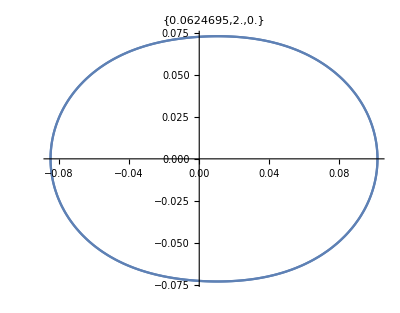
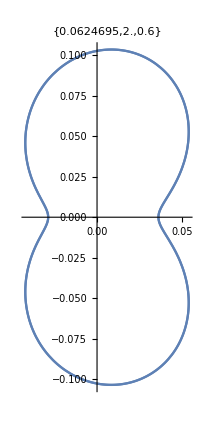
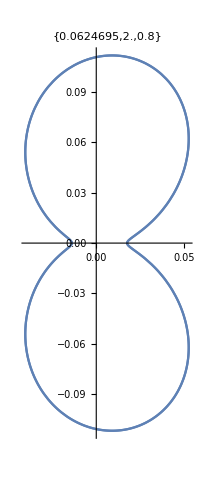
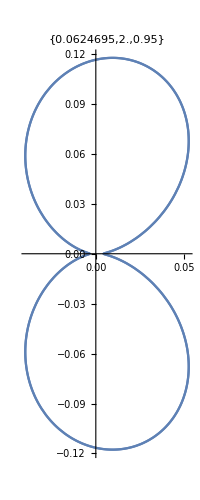
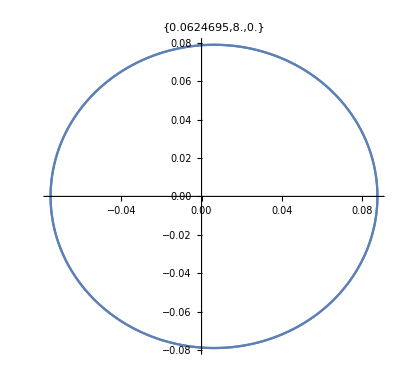
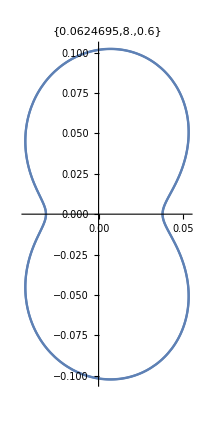
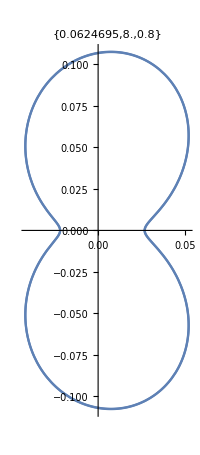
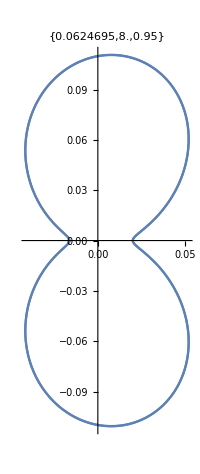
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[PolarPlot[{S[θ,j],Acosta[θ,kissel[[j,1]],AA, BB]}/.bestAB[[j]],{θ,-π,π},PlotLabel->N[kissel[[j,{1,2,3}]]],DisplayFunction->Identity],{j,1,144}],4]]
```

```mathematica
kissel=Partition[Flatten[Riffle[kissel,{AA,BB}/.bestAB]],11];
```

```mathematica
kisselByElm=Flatten[Function[z,Select[kissel,Part[#,2]==z&]]/@{2,8,13,47,79,92},1];
```

```mathematica
Plot A in a rationalized order
```

a A in order Plot rationalized

```mathematica
Grid[Partition[Table[ListPlot[Table[{kissel[[j,1]],kissel[[j,1]]kissel[[j,10]]},{j,1+Mod[k*4+Floor[k/6],24],141,24}],{Joined->True,PlotLabel->{ kissel[[1+Mod[k*4+Floor[k/6],24],2]],kissel[[1+Mod[k*4+Floor[k/6],24],3]]},{AxesLabel->{"β","Aβ"}}},DisplayFunction->Identity],{k,0,23}],6]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Plot B in a rationalized order
```

a B in order Plot rationalized

```mathematica
Grid[Partition[Table[ListPlot[Table[{kissel[[j,1]],kissel[[j,1]] kissel[[j,11]]},{j,1+Mod[k*4+Floor[k/6],24],141,24}],{Joined->True,PlotLabel->{ kissel[[1+Mod[k*4+Floor[k/6],24],2]],kissel[[1+Mod[k*4+Floor[k/6],24],3]]},{AxesLabel->{"β","βB"}}},DisplayFunction->Identity],{k,0,23}],6]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-